```mathematica
D[3x^2-4x,x]
```

-4+6 x

```mathematica
D[x^n,x]
```

n x^(-1+n)

```mathematica
D[(1+5x)^3,x]
```

15 (1+5 x)^2

```mathematica
z=t^2+Sin[5t]
```

t^2+Sin[5 t]

```mathematica
D[z,{t,2}]
```

2-25 Sin[5 t]

```mathematica
D[5*x^2+3*x*y-2*y^2+2,y]
```

3 x-4 y

```mathematica
x=a
```

a

```mathematica
D[x^(2/3)+y^(2/3),y]==a^(2/3)
```

2/(3 y^(1/3))==a^(2/3)

```mathematica
D[Sqrt[x],x]
```

1/(2 √a)

```mathematica
D[x^(1/2),x]
```

1/(2 √a)

```mathematica
D[(3*Sin^2[x]+Cos[x])/(Log10[8x^2]),x]
```

-(2 (3 Sin^(2[a])+Cos[a]) Log[10])/(a Log[8 a^2]^2)-(Log[10] Sin[a])/Log[8 a^2]

```mathematica
Integrate[x^4,x]
```

a^5/5

```mathematica
Integrate[E^(4x),x]
```

ⅇ^(4 a)/4

```mathematica
Integrate[Cos[x/2]Cos[3x/2],{x,0,Pi}]
```

0

```mathematica
Limit[Sin[4x]/Sin[3x],x->0]
```

4/3

```mathematica
Limit[Sqrt[3x]/x,x->0]
```

Indeterminate

```mathematica
Infinity
```

∞

```mathematica
Solve[3x+4==0]
```

{{a→-4/3}}

```mathematica
Solve[10x==4]
```

{{a→2/5}}

```mathematica
Solve[3x+4y==0 && 6x-3y==4,{x,y}]
```

{{a→16/33,y→-4/11}}

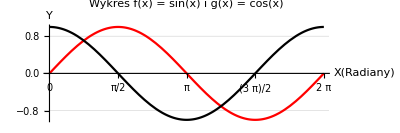

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,2 Pi},AxesLabel->{StyleForm["X(Radiany)",FontSize->14,Red],StyleForm["Y",FontSize->12,Green]},PlotLabel->Style[Framed["Wykres f(x) = sin(x) i g(x) = cos(x)"],15,Bold,Frame->False,Blue,Background->Lighter[Green]],PlotLegends->{"sin(x)","cos(x)"},PlotStyle->{Red,Black},PlotStyle->Dashed,GridLines->Automatic,Ticks->{Range[0,2Pi,Pi/4],Automatic},AspectRatio->1/3]
```

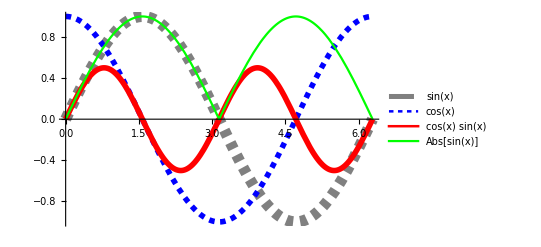

```mathematica
Plot[{Sin[x],Cos[x],Cos[x]Sin[x],Abs[Sin[x]]},{x,0,2Pi},PlotLegends->"Expressions",PlotStyle->{{Gray,Dashed,Thickness[0.02]},{Blue,Dashing[0.01],Thickness[0.01]},{Red,Thickness[0.01]},{Green}}]
```

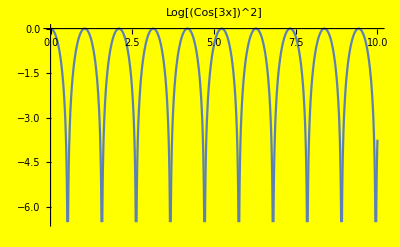

```mathematica
Plot[Log[(Cos[3x])^2],{x,0,10},Background->Yellow,PlotLabel->Style["Log[(Cos[3x])^2]",Directive[Blue,Blod]],ImagePadding->{{50,10},{PlotLabel,PlotLabel}}]
```

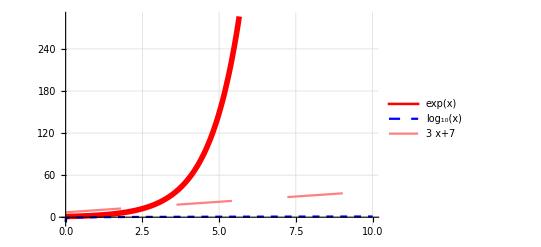

```mathematica
Plot[{Exp[x],Log10[x],3x+7},{x,0,10},PlotLegends->"Expressions",GridLines->Automatic,PlotStyle->{{Red,Thickness[0.01]},{Blue,Dashed},{Pink,Dashing[0.1]}}]
```

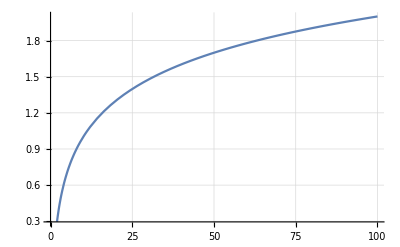

```mathematica
Plot[Log10[x],{x,0,100},GridLines->Automatic]
```

```mathematica
listaPunktow = {{-2,-1},{-1,0},{0,0.75},{1,1},{2,0},{1,-1},{0,-0.75},{-1,0},{-2,1}};
```

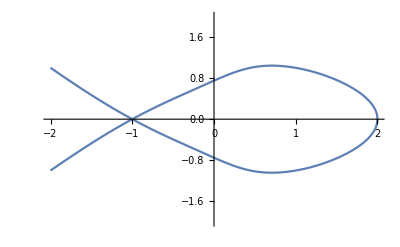

```mathematica
wykres = ListPlot[listaPunktow,PlotRange->{-2,2},Joined->True,InterpolationOrder->4
,ImageSize->Scaled[0.3]]
```

```mathematica
Show[Interpolation[listaPunktow],{x,-2,2}],Graphics[{Red,Line[listaPunktow]}]
```

```mathematica
punkty={{0,1},{1,0},{3,1}};
```

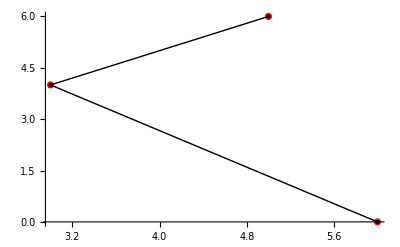

```mathematica
(*wykres=ListPlot[punkty,PlotStyle->Red];
polaczone=Graphics[{Line[punkty],PointSize[Large],Point[punkty]}];
Show[wykres,polaczone]*)
```

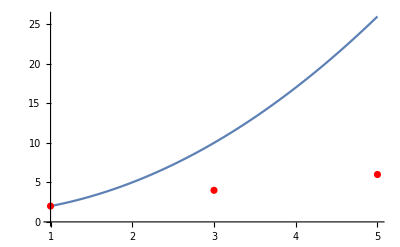

```mathematica
funkcjaInterpolujaca=Interpolation[punkty,InterpolationOrder->1];
wykres=Plot[funkcjaInterpolujaca[x^2],{x,1,5}];
Show[wykres,ListPlot[punkty,PlotStyle->Red]]
```

```mathematica
lista = {{-2,4},{-1,1},{0,0},{1,1},{2,4}};
```

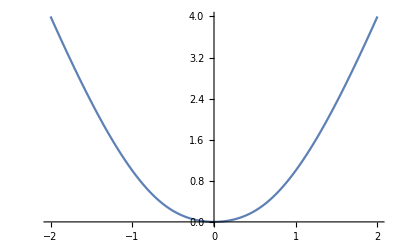

```mathematica
ListPlot[lista,Joined->True,InterpolationOrder->4]
```

```mathematica
Plot3D[{Tan[x]Sin[Log[x]2x^2-y^2*8x+Abs[2-y^3]]},{x,0,10},{y,0,10},Boxed->False,Mesh->None,ColorFunction->"TemperatureMap"]
```

-Graphics3D-

```mathematica
27^(1/3)
```

3

```mathematica
wyniki={};
```

```mathematica
{}
```

{}

```mathematica
wyniki={};
For[i=1,i≤10,i++,AppendTo[wyniki,2i]]
```

```mathematica
wyniki
```

{2,4,6,8,10,12,14,16,18,20}